## First lecture - Mathematica recap

```mathematica
Clear["Global`*"]
```

```mathematica
a = 5
```

5

```mathematica
a = 5;
```

The assignement of variable cna be “set assignement” as the last one or the “set delay” (something like that) that is handy when we use functions. It evaluates the variable when we call it, not everytime like using hte set assignement

```mathematica
r := RandomReal[]
r
Print[r, " ", a]
```

0.924978

We can define vectors using curly brackets and separating numbers with a comma. For wolfram there are no differences between row vector and column vector. There is the function matrixform in roder to check better the matrix visually. Call it using MatrixForm[A] or A // MatrixForm, it’s the same.
For the moltiplication, the dot is the symbol

```mathematica
v = {1, 2, 3};
A = {{1, 2, 3}, {4, 5, 6}, {8, 8, 9}};
MatrixForm[A];
A // MatrixForm
Det[A]
Amin = Inverse[A]; 
Amin // MatrixForm
Atransp = Transpose[A];
Atransp // MatrixForm

A.v // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
8 | 8 | 9)

-3

(1 | -2 | 1
-4 | 5 | -2
8/3 | -8/3 | 1)

(1 | 4 | 8
2 | 5 | 8
3 | 6 | 9)

(14
32
51)

There is a way to draw manipiulators here

```mathematica
Graphics3D[
 {
   Thickness[0.01],
   Red,
   Arrowheads[0.07],
   Arrow[{{0, 0, 0}, {1, 2, 3}}],
   Text["vector", {1, 2, 3}]
 },
 Axes -> True,
 PlotRange -> {{0, 4}, {0, 4}, {0, 4}}
]
```

-Graphics3D-

Let’s define functions, in this case for defining skew symmetric matrices. A matrix is skew symmetric if it’s equal to the negative of its transpose.
For the function we use the set delay because we don’t want to assign the value.  Using [[ to select values in a vector.
A good check for the skew symmetric SkewMat + Transpose[SkewMat] // MatrixForm and the result should be all zeros.

```mathematica
skew[w_] := {{0, -w[[3]], w[[2]]}, {w[[3]], 0, w[[1]]}, {-w[[2]], -w[[1]], 0}};
Vtest1 = {1, 3, -7};
Vtest2 = {q, j, g};
SkewMat = skew[Vtest1];
SkewMat // MatrixForm 
SkewMatGen2 = skew[Vtest2];
SkewMatGen2 // MatrixForm

SkewMat + Transpose[SkewMat] // MatrixForm

skew[Vtest1].Vtest1
```

(0 | 7 | 3
-7 | 0 | 1
-3 | -1 | 0)

(0 | -g | j
g | 0 | q
-j | -q | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

{0,-14,-6}

```mathematica
v = {v1, v2, v3}
k = {k1, k2, k3}
z1 = Cross[v, k]
z2 = skew[v].k
z2-z1
```

{v1,v2,v3}

{k1,k2,k3}

{k3 v2-k2 v3,-k3 v1+k1 v3,k2 v1-k1 v2}

{k3 v2-k2 v3,k3 v1+k1 v3,-k2 v1-k1 v2}

{0,2 k3 v1,-2 k2 v1}

Solve differential equations. With Solve the result will be displayed as fractions, with NSolve it will be displayed numerically. Doing a = x + 5y;
a /. {y -> 2} means that if y is not assigned a is parametric with respect to y and we change temporary the value of the parameter y, not globally (?).
We can solve differential equations even with starting conditions with DSolve.

When we make a product between scalars we use *
When we make a product between vectors and matrices we use .

```mathematica
Solve[x^2 - 5 x + 6 == 0, x]

Solve[{2x + y == 10, x - y == 1}, {x, y}]
a = x + 5y;
a /. {y -> 2}
```

{{x→2},{x→3}}

{{x→11/3,y→8/3}}

10+x

```mathematica
DSolve[{x'[t] == -x[t], x[0] == 1}, x[t], t]
```

{{x[t]→ⅇ^-t}}

### Example with RC differential equation

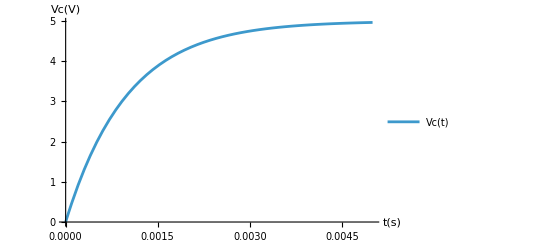

```mathematica
R = 1000; (*ohm*)
Cap = 1.*10^-6; (*farad*)
tau = R * Cap;
Vin[t_] = 5UnitStep[t];
eq = R * Cap * Vc'[t] + Vc[t] == Vin[t];

sol = NDSolve[{eq, Vc[0] == 0}, Vc[t], {t, 0, 5 * tau}];
Plot[Vc[t] /.sol, {t, 0, 5 * tau}, PlotLegends -> {"Vc(t)"}, AxesLabel->{"t(s)", "Vc(V)"}, PlotRange->All]
```

#### Spring Mass Damper example

{{x→InterpolatingFunction[…]}}

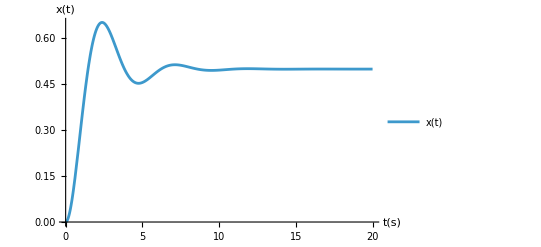

```mathematica
m = 1;
c = 1;
k = 2;

F[t_] = 1UnitStep[t];
eq = m x''[t] + c x'[t] + k x[t] == F[t];
sol = NDSolve[{eq, x[0] == 0, x'[0] == 0}, x, {t, 0, 20}]
Plot[x[t] /.sol, {t, 0, 20}, AxesLabel->{"t(s)", "x(t)"}, PlotLegends->{"x(t)"}, PlotRange->All]
```